## old stuff

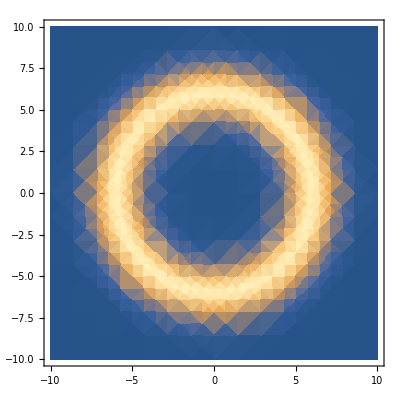

```mathematica
DensityPlot[Exp[-((6-√(x^2+y^2))^2)/(2*1^2)],{x,-10,10},{y,-10,10},PlotRange->Full]
```

```mathematica
Integrate[Exp[(-(μ-r)^2)/(2*σ^2)]^2,{r,0,∞},{ϕ,0,2π},Assumptions->{σ>0,μ>0}]
```

π^(3/2) σ (1+Erf[μ/σ])

```mathematica
PsiSingleUnNormalised=Exp[-(x3-μ3x)^2/(2*σ3x^2)-(z3-μ3z)^2/(2*σ3z^2)]*Exp[ⅈ/ℏ*p3*√(x3^2+z3^2)]*Exp[-(x4-μ4x)^2/(2*σ4x^2)-(z4-μ4z)^2/(2*σ4z^2)]*Exp[ⅈ/ℏ*p4*√(x4^2+z4^2)]
```

ⅇ^(-(x3-μ3x)^2/(2 σ3x^2)-(z3-μ3z)^2/(2 σ3z^2)-(x4-μ4x)^2/(2 σ4x^2)-(z4-μ4z)^2/(2 σ4z^2)+(ⅈ p3 √(x3^2+z3^2))/ℏ+(ⅈ p4 √(x4^2+z4^2))/ℏ)

```mathematica
PsiSingleUnNormalisedSimplified=Exp[-(x3-μ3x)^2/(2*σ3x^2)-(z3-μ3z)^2/(2*σ3z^2)]*Exp[-(x4-μ4x)^2/(2*σ4x^2)-(z4-μ4z)^2/(2*σ4z^2)];
```

```mathematica
Integrate[Conjugate[PsiSingleUnNormalisedSimplified]*PsiSingleUnNormalisedSimplified,
{x3,-∞,∞},{z3,-∞,∞},{x4,-∞,∞},{z4,-∞,∞},Assumptions->{σ3x>0,σ3z>0,σ4x>0,σ4z>0,μ3x∈Reals,μ3z∈Reals,μ4x∈Reals,μ4z∈Reals}]
```

$Aborted

```mathematica
PsiSingle=1/(π √(σ3x σ3z σ4x σ4z))Exp[-(x3-μ3x)^2/(2*σ3x^2)-(z3-μ3z)^2/(2*σ3z^2)]*Exp[ⅈ/ℏ*p3*√(x3^2+z3^2)]*Exp[-(x4-μ4x)^2/(2*σ4x^2)-(z4-μ4z)^2/(2*σ4z^2)]*Exp[ⅈ/ℏ*p4*√(x4^2+z4^2)];
```

```mathematica
PsiSingleInRing[ϕ_]:=Simplify[Evaluate[PsiSingle/.{μ3x->r*Cos[ϕ],μ3z->r*Sin[ϕ],μ4x->3/4 r*Cos[ϕ],μ4z->3/4 r*Sin[ϕ],p4->p,p3->p,σ3x->σr,σ3z->σr,σ4x->σr,σ4z->σr}],Assumptions->{σr>0}];
PsiSingleInRing[ϕ]
```

(ⅇ^((32 ⅈ p √(x3^2+z3^2) σr^2+32 ⅈ p √(x4^2+z4^2) σr^2-25 r^2 ℏ-16 x3^2 ℏ-16 x4^2 ℏ-16 z3^2 ℏ-16 z4^2 ℏ+8 r (4 x3+3 x4) ℏ Cos[ϕ]+8 r (4 z3+3 z4) ℏ Sin[ϕ])/(32 σr^2 ℏ)))/(π σr^2)

```mathematica
PsiPair[ϕ_]:=1/(√2)(PsiSingleInRing[ϕ]+PsiSingleInRing[ϕ+π])
```

```mathematica
Integrate[1/(√(2π))PsiPair[ϕ],{ϕ,0,2π}]
```

$Aborted

https://www.desmos.com/calculator/dscl9tkf4f

```mathematica
FullSimplify[1/4(1-ⅈ ⅇ^(ⅈ(ϕ+α)))*(1+ⅈ ⅇ^(-ⅈ(ϕ+α)))]
```

1/2 (1+Sin[α+ϕ])

```mathematica
FullSimplify[1/4(ⅇ^(ⅈ ϕ)-ⅈ ⅇ^(-ⅈ α))*(ⅇ^(-ⅈ ϕ)+ⅈ ⅇ^(+ⅈ α))]
```

1/2 (1-Sin[α+ϕ])

```mathematica
(1/2 (1+Sin[α+ϕ]))+1/2 (1-Sin[α+ϕ])//FullSimplify
```

1

## copied over

```mathematica
cU=Quantity["SpeedOfLight"];
```

```mathematica
hU=Quantity["PlanckConstant"];
ℏU=Quantity["ReducedPlanckConstant"];
```

```mathematica
UnitConvert[ℏU,"u * micrometers^2 * ms^-1"]
```

63.5077993 u μm^2/ms

```mathematica
ℏM=QuantityMagnitude[ℏU,"u * mm^2 * ms^-1"]
```

0.0000635077993

```mathematica
l0U=Quantity[858.7,"mm"];
gU=Quantity[9.796,"Meters*Seconds^-2"];
t0U=√((2*l0U)/gU);
t0M=QuantityMagnitude[t0U,"ms"]
```

418.708

```mathematica
m4U=Entity["Isotope","Helium4"][EntityProperty["Isotope","AtomicMass"]];
m3U=Entity["Isotope","Helium3"][EntityProperty["Isotope","AtomicMass"]];
m4M=QuantityMagnitude[m4U]
m3M=QuantityMagnitude[m3U]
```

4.002603254

3.016029322

```mathematica
λU=Quantity[1083,"nm"];
νU=UnitConvert[cU/λU,"THz"]//N;
ωU=2*π*νU;
```

```mathematica
pCU=UnitConvert[(νU*hU)/cU,"eV/c"]
UnitConvert[pCU,"u * mm * s^-1"]
pCM=QuantityMagnitude[pCU,"u * microm * ms^-1"];
```

1.14482 eV/c

368.45 u mm/s

```mathematica
v4U=UnitConvert[pCU/m4U,"microm * ms^-1"];
v4M=QuantityMagnitude[v4U]
v3U=UnitConvert[pCU/m3U,"microm * ms^-1"];
v3M=QuantityMagnitude[v3U]
```

92.0526

122.164

```mathematica
UnitConvert[λU,"mm"]//N
```

0.001083 mm

```mathematica
UnitConvert[(1-1/(√(1-(v3U/cU)^2)))*νU,"Hz"]
```

0. Hz

```mathematica
UnitConvert[(v3U^2*m3U)/ℏU,"per ms"]
```

708.752 /ms

```mathematica
a34U=Quantity[29,"Nanometers"];
```

```mathematica
UnitConvert[a34U,"Micrometers"]//N
```

0.029 μm

```mathematica
UnitConvert[cU/λU,"THz"]//N
```

276.817 THz

```mathematica
UnitConvert[cU/λU*ℏU,"u*"]//N
```

2.91923×10^-20 kg m^2/s^2

### doppler?

```mathematica
UnitConvert[((cU+v4U)/cU)*(νU)-(νU),"kHz"]
```

84.9977 kHz

```mathematica
UnitConvert[((cU+v4U*2/(√2))/cU)*(νU*2/(√2))-(νU*2/(√2)),"kHz"]
```

169.996 kHz

```mathematica
UnitConvert[(v4U*(√2))/cU*(νU*√2),"kHz"]
```

169.996 kHz

```mathematica
UnitConvert[v4U/cU*(νU),"kHz"]
```

84.9978 kHz

```mathematica
UnitConvert[1/(2π)(ℏU*((2π)/λU)^2)/m4U,"kHz"]
```

84.9977588 kHz

```mathematica
UnitConvert[1/(2π)(ℏU*((2π)/λU*2/(√2))^2)/m4U,"kHz"]
```

169.995518 kHz

```mathematica
UnitConvert[1/(2π)(ℏU*((2π)/Quantity[1083.1927,"nm"])^2)/m4U,"kHz"]
```

84.9675 kHz

```mathematica
Quantity[84.96751930462096, "Kilohertz"]/2
```

42.4838 kHz

```mathematica
UnitConvert[1/(2π)(ℏU*((2π)/Quantity[1083.1927,"nm"] 2/(√2))^2)/m4U,"kHz"]
```

169.935 kHz

```mathematica
UnitConvert[1/(2π)(ℏU*((2π)/Quantity[1083.1927,"nm"] 2/(√2))^2)/m4U,"kHz"]/2
```

84.9675 kHz

```mathematica
UnitSimplify[(2π)/λU]
```

(2 π)/1083 /nm

## Fall time

```mathematica
UnitConvert[v4U,"cm/s"]
```

9.20526 cm/s

```mathematica
UnitConvert[v4U*√2,"cm/s"]
```

13.0182 cm/s

```mathematica
√((2*l0U)/gU)
```

0.418708 s

```mathematica
Solve[1/2*gU*t^2+v4U*√2*t==l0U,t]
```

{{t→-0.432208 s},{t→0.40563 s}}

```mathematica
Quantity[0.40562961819577764, "Seconds"]-Quantity[0.41870807932998205, "Seconds"]
```

-0.0130785 s

So should arrive 13ms before/after for each √2 ℏk

```mathematica
Solve[1/2*gU*t^2-v4U*√2*t==l0U,t]
```

{{t→-0.40563 s},{t→0.432208 s}}

```mathematica
Quantity[0.43220822107616863, "Seconds"]-Quantity[0.41870807932998205, "Seconds"]
```

0.0135001 s

```mathematica
UnitConvert[v4U*t0U,"cm"]
```

3.85432 cm

```mathematica
UnitConvert[v4U*Quantity[{0.1,0.2,0.3,0.4},"s"],"cm"]
```

{0.920526 cm,1.84105 cm,2.76158 cm,3.6821 cm}

```mathematica
UnitConvert[Quantity[160,"microm"]/v4U,"ms"]
```

1.73814 ms

```mathematica
kU=(2π)/λU;
```

```mathematica
UnitConvert[(kU^2 ℏU)/(2m4U),"kHz"]
```

267.028335 kHz

```mathematica
νU
```

276.817 THz

```mathematica
UnitConvert[1/(√2((kU^2 ℏU)/(2m4U))),"micros"]
```

2.64805899 μs

```mathematica
UnitSimplify[ℏU/Quantity[2.6480589860689879204`9.166112448093052, "Microseconds"]]
```

2.48563933×10^-7 meV

```mathematica
UnitSimplify[ℏU*Quantity[84.99773684889078, "Kilohertz"]]
```

5.59465×10^-8 meV

```mathematica
UnitSimplify[ℏU/Quantity[50,"micros"]]//N
```

1.31642×10^-8 meV

```mathematica
UnitSimplify[l0U/v4U]
```

9.32837 s

```mathematica
UnitSimplify[t0U*v4U]
```

3.85432 cm

```mathematica
UnitSimplify[0.5*gU*t0U^2]
```

0.8587 m

```mathematica
UnitSimplify[0.5*gU*t0U^2+t0U*v4U]
```

0.897243 m

```mathematica
Solve[l0U==v4U*t+1/2*gU*t^2,t]
```

{{t→-0.42821 s},{t→0.409417 s}}

```mathematica
t0U
```

0.418708 s

```mathematica
UnitConvert[Quantity[0.41870807932998205, "Seconds"]-Quantity[0.4094165575851127, "Seconds"],"ms"]
```

9.29152 ms

```mathematica
Exp[-(x3-μ3x)^2/(2*σ3x^2)-(z3-μ3z)^2/(2*σ3z^2)]*Exp[-(x4-(-3/4 μ3x))^2/(2*σ4x^2)-(z4-(-3/4 μ4z))^2/(2*σ4z^2)]
```

ⅇ^(-(x3-μ3x)^2/(2 σ3x^2)-(z3-μ3z)^2/(2 σ3z^2)-(x4+(3 μ3x)/4)^2/(2 σ4x^2)-(z4+(3 μ4z)/4)^2/(2 σ4z^2))

```mathematica
Exp[-(x3-μ3x)^2/(2*σ3x^2)-(z3-μ3z)^2/(2*σ3z^2)]*Exp[-(x4-(-3/4 μ3x))^2/(2*σ4x^2)-(z4-(-3/4 μ3z))^2/(2*σ4z^2)]/.{μ3x->r*Cos[ϕ],μ3z->r*Sin[ϕ]}
```

ⅇ^(-(x3-r Cos[ϕ])^2/(2 σ3x^2)-(x4+3/4 r Cos[ϕ])^2/(2 σ4x^2)-(z3-r Sin[ϕ])^2/(2 σ3z^2)-(z4+3/4 r Sin[ϕ])^2/(2 σ4z^2))

```mathematica
Integrate[ⅇ^(-(x3-r Cos[ϕ])^2/(2 σ3x^2)-(x4+3/4 r Cos[ϕ])^2/(2 σ4x^2)-(z3-r Sin[ϕ])^2/(2 σ3z^2)-(z4+3/4 r Sin[ϕ])^2/(2 σ4z^2)),{ϕ,0,2π},Assumptions->{σ3x>0,σ3z>0,σ4x>0,σ4z>0}]
```

$Aborted

```mathematica
Exp[-(r3^2+μr3^2-2*r3*μr3*Cos[ϕ3-μϕ3])/(2*σr3^2)]*Exp[-(r4^2+μr4^2-2*r4*μr4*Cos[ϕ4-μϕ4])/(2*σr4^2)]/.{μr4->3/4 μr3,μϕ4->-μϕ3}
```

ⅇ^(-(r3^2+μr3^2-2 r3 μr3 Cos[μϕ3-ϕ3])/(2 σr3^2)-(r4^2+(9 μr3^2)/16-3/2 r4 μr3 Cos[μϕ3+ϕ4])/(2 σr4^2))

```mathematica
Integrate[ⅇ^(-(r3^2+μr3^2-2 r3 μr3 Cos[μϕ3-ϕ3])/(2 σr3^2)-(r4^2+(9 μr3^2)/16-3/2 r4 μr3 Cos[μϕ3+ϕ4])/(2 σr4^2)),{μϕ3,0,2π},Assumptions->{σ3x>0,σ3z>0,σ4x>0,σ4z>0}]
```

∫_0^(2 π) ⅇ^(-(r3^2+μr3^2-2 r3 μr3 Cos[μϕ3-ϕ3])/(2 σr3^2)-(r4^2+(9 μr3^2)/16-3/2 r4 μr3 Cos[μϕ3+ϕ4])/(2 σr4^2))ⅆμϕ3